Probability of l<b without branch

```mathematica
P1[l_,p_]:=p^l*(1-p)
```

Probability of b<=l<L

```mathematica
P2[l_,p_]:=p^l*(1-p)^2
```

Probability of l=L

```mathematica
P3[L_,p_]:=p^L*(1-p)
```

Probability of b<=l<L with branch

```mathematica
P4[l_,p_]:=p^(l+1)*(1-p)
```

Probability of b=L with branch

```mathematica
P5[L_,p_]:=p^(L+1)
```

```mathematica
S1[b_,p_]:=Sum[P1[l,p]*Log[P1[l,p]],{l,0,b-1}]
S2[L_,b_,p_]:=Sum[P2[l,p]*Log[P2[l,p]],{l,b,L-1}]
S3[L_,b_,p_]:=Sum[P4[l,p]*Log[P4[l,p]],{l,b,L-1}]
Em[L_,b_,p_]:=-(S1[b,p]+S2[L,b,p]+S3[L,b,p]+P3[L,p]*Log[P3[L,p]]+P5[L,p]*Log[P5[L,p]])
```

```mathematica
S4[L_,p_]:=Sum[P1[l,p]*Log[P1[l,p]],{l,0,L-1}]
```

```mathematica
Em2[L_,p_]:=-(S4[L,p]+p^L*Log[p^L])
```

This is my equation for entropy that I calculated using geometric and arithmetic sums. I does not match the above

```mathematica
En[L_,b_,p_]:=(1-p)(Log[1-p]*(1-p^b)/(1-p)+Log[p]*((b-1)p^b/(1-p)+p(1-p^(b-1))/(1-p)^2))+(1-p)^2(p^b(1-p^(L-b))/(1-p)Log[(1-p)^2] +Log[p]((L-1)*p^L/(1-p)+p(1-p^(L-1))/(1-p)^2-(b-1)p^b/(1-p)-p(1-p^(b-1))/(1-p)^2))+(1-p)*(Log[1-p]*p^(b+1)(1-p^(L-b))/(1-p)+Log[p]+p(1-p^L)/(1-p)^2+L*p^(L+1)/(1-p)-p(1-p^b)/(1-p)^2+b*p^(L+1)/(1-p))+p^L*(1-p)Log[p^L*(1-p)]+p^(L+1)*Log[p^(L+1)]
```

Adjusted rates

```mathematica
h[τ_]:=1/(1+1/τ)
```

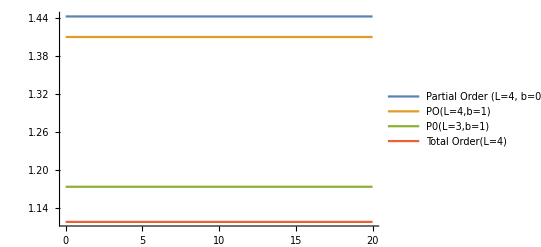

```mathematica
Plot[{Em[4,0,h[τ]],Em[4,1,h[τ]],Em[3,1,h[τ]],Em2[4,h[τ]]},{τ,0,20},PlotLegends->{"Partial Order (L=4, b=0)","PO(L=4,b=1)","P0(L=3,b=1)","Total Order(L=4)"}]
```

```mathematica
T1=Evaluate@Table[Em[4,b,h[τ]],{b,0,3}];
```

```mathematica
T2=Evaluate@Table[Em[3,b,h[τ]],{b,0,2}];
```

```mathematica
T3=Evaluate@Table[Em[2,b,h[τ]],{b,0,1}];
```

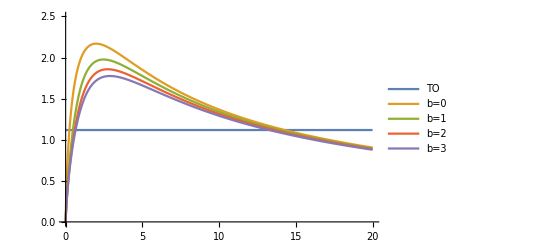

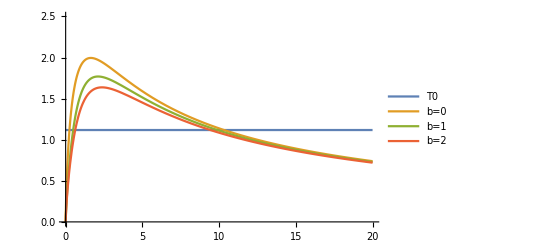

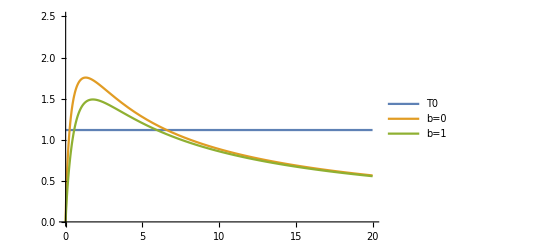

```mathematica
Plot[{Em2[4,h[τ]],T1},{τ,0,20},PlotRange->{0,2.5} ,PlotLegends->{"TO","b=0","b=1","b=2","b=3"}]
Plot[{Em2[4,h[τ]],T2},{τ,0,20},PlotRange->{0,2.5} ,PlotLegends->{"T0","b=0","b=1","b=2"}]
Plot[{Em2[4,h[τ]],T3},{τ,0,20},PlotRange->{0,2.5} ,PlotLegends->{"T0","b=0","b=1"}]
```

```mathematica
Ln=4;
Br=2;
```

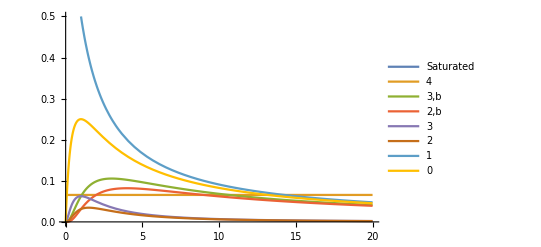

(1-1/(1+1/τ))/(1+1/τ)^4

(1-1/(1+1/τ))/(1+1/τ)^4

```mathematica
T4=Evaluate@Table[P1[l,h[τ]],{l,0,Br-1}];
T5=Evaluate@Table[P2[l,h[τ]],{l,Br,Ln-1}];
T6=Evaluate@Table[P4[l,h[τ]],{l,Br,Ln-1}];
Plot[{P5[Ln,h[τ]],P3[Ln,h[τ]],T6,T5,T4},{τ,0,20},PlotRange->{0,0.5},PlotLegends->{"Saturated","4","3,b","2,b","3","2","1","0"}]
T6[[2]]
P3[Ln,h[τ]]
```

```mathematica
NT4=Length[T4];
NT5=Length[T5];
NT6=Length[T6];
```

```mathematica
TT42=Evaluate@Table[Sum[T4[[{i}]],{i,1,j}],{j,1,NT4}];
TT52=Evaluate@Table[TT42[[NT4]]+Sum[T5[[{i}]],{i,1,j}],{j,1,NT5}];
TT62=Evaluate@Table[TT52[[NT5]]+Sum[T6[[{i}]],{i,1,j}],{j,1,NT6}];
CU1[L_,τ_]:=TT62[[NT6]]+P3[L,h[τ]];
CU2[L_,τ_]:=CU1[L,τ]+P5[L,h[τ]];
```

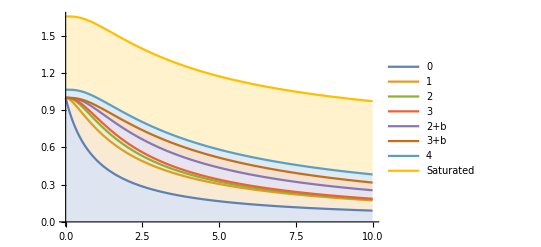

```mathematica
Plot[{TT42,TT52,TT62,CU1[Ln,τ],CU2[Ln,τ]},{τ,0,10},PlotLegends->{"0","1","2","3","2+b","3+b","4","Saturated"}, Filling->{1->Axis,2->{1},3->{2},4->{3},5->{4},6->{5},7->{6},8->{7}}]
```

```mathematica
T43=Evaluate@Table[τ/.Solve[P1[i,h[τ]]==1/20&& τ>0],{i,0,Br-1}]
```

{{19},{9-4 √5,9+4 √5}}

```mathematica
T53=Evaluate@Table[τ/.Solve[P2[i,h[τ]]==1/20&& τ>0],{i,Br,Ln-1}]
```

{{Root[1+4 #1-14 #1^2+4 #1^3+#1^4&,3],Root[1+4 #1-14 #1^2+4 #1^3+#1^4&,4]},τ}

```mathematica
T63=Evaluate@Table[τ/.Solve[P4[i,h[τ]]==1/20&& τ>0],{i,Br,Ln-1}]
```

{{Root[1+4 #1+6 #1^2-16 #1^3+#1^4&,1],Root[1+4 #1+6 #1^2-16 #1^3+#1^4&,2]},{Root[1+5 #1+10 #1^2+10 #1^3-15 #1^4+#1^5&,2],Root[1+5 #1+10 #1^2+10 #1^3-15 #1^4+#1^5&,3]}}

```mathematica
L1=τ/.Solve[P3[Ln,h[τ]]==1/20&&τ>0]
```

{Root[1+5 #1+10 #1^2+10 #1^3-15 #1^4+#1^5&,2],Root[1+5 #1+10 #1^2+10 #1^3-15 #1^4+#1^5&,3]}

```mathematica
L2=τ/.Solve[P5[Ln,h[τ]]==1/20&&τ>0]
```

{Root[-1-5 #1-10 #1^2-10 #1^3-5 #1^4+19 #1^5&,1]}

Is there any way to make this faster...to make a table of these?

```mathematica
a[x_]:=0.2/;x<19
b[x_]:=0.3/;T43[[2]][[1]]<x<T43[[2]][[2]]
c[x_]:=0.4/;T53[[1]][[1]]<x<T53[[1]][[2]]
d[x_]:=0;
e[x_]:=0.6/;T63[[1]][[1]]<x<T63[[1]][[2]]
f[x_]:=0.7/;T63[[2]][[1]]<x<T63[[2]][[2]]
g[x_]:=0.8/;L1[[1]]<x<L1[[2]]
h[x_]:=0.9/;L2[[1]]x<22
```

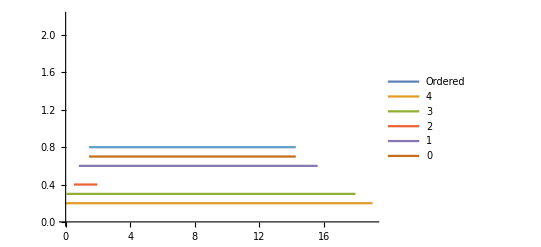

```mathematica
Plot[{Em[x,4],a[x],b[x],c[x],e[x],f[x],g[x]},{x,0,21},PlotRange->{0,2.2},PlotLegends->{"Ordered","4","3","2","1","0"}]
```

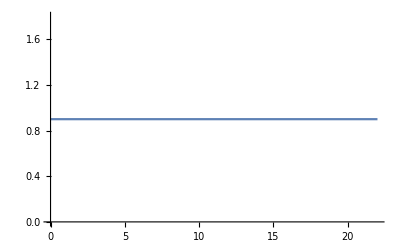

```mathematica
Plot[h[x],{x,0,22}]
```